Autor: Jhordan Silveira de Borba (sbjhordan@gmail.com)
Site: https://sites.google.com/view/jdan/

## Equações originais

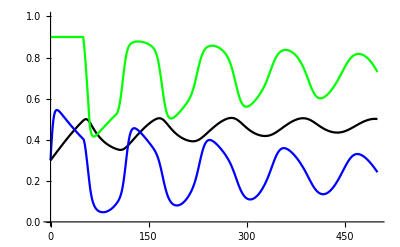

```mathematica
(* Valor de destrucción fijo. Ver más abajo Manipulate. *)
parametros={c1->0.04,c2->0.7,e1->0.01,e2->0.01,g->0.1};tr=10;to=50;h0=0.9;x10=0.3;x20=0.3;
tmax=500;
dsol1=NDSolve[{
c1 x11[t](h0-x11[t])-e1 x11[t]==x11'[t],
c2 x21[t](h0-x11[t]-x21[t])-e2 x21[t]==x21'[t],
x11[0]==x10,x21[0]==x20}/.parametros,{x11,x21},{t,0,to}/.parametros, StartingStepSize->0.001,MaxStepSize->0.001];
(*Plot[{x11[t]/.dsol1,x21[t]/.dsol1},{t,0,to/.parametros},PlotRange->{0,1.},PlotStyle->{Black,Blue}]*)
dsol2=NDSolve[{
c1 x12[t](h2[t]-x12[t])-e1 x12[t]==x12'[t],
c2 x22[t](h2[t]-x12[t]-x22[t])-e2 x22[t]==x22'[t],
-g*x22[t-to]*h2[t-to]==h2'[t],
x12[t/;t≤to]==x11[t]/.dsol1,x22[t/;t≤to]==x21[t]/.dsol1,h2[t/;t≤to]==h0}/.parametros,
{x12,x22,h2},{t,0,to+tr}, StartingStepSize->0.001,MaxStepSize->0.0001];
(*Plot[{x12[t]/.dsol2,x22[t]/.dsol2,h2[t]/.dsol2},{t,0,to+tr},PlotRange->{0,1.},PlotStyle->{Black,Blue, Green}]*)
dsol=NDSolve[{
c1 x1[t](h[t]-x1[t])-e1 x1[t]==x1'[t],
c2 x2[t](h[t]-x1[t]-x2[t])-e2 x2[t]==x2'[t],
-g*x2[t-to]*h[t-to]+g*x2[t-to-tr]*h[t-to-tr]==h'[t],
x1[t/;t≤to+tr]==x12[t]/.dsol2,x2[t/;t≤to+tr]==x22[t]/.dsol2,h[t/;t≤to+tr]==h2[t]/.dsol2}/.parametros,{x1,x2,h},{t,0,tmax}, StartingStepSize->0.001,MaxStepSize->0.001];

Plot[{x1[t]/.dsol,x2[t]/.dsol,h[t]/.dsol},{t,0,tmax},PlotRange->{0,1.},PlotStyle->{Black,Blue,Green}]
```

### Análise analítica

```mathematica
parametros={c1->0.04,c2->0.7,e1->0.01,e2->0.01,tr->10,to->50,g->0.1};
dx1=(c1* x1(h-x1)-e1 x1);
dx2=(c2 x2(h-x1-x2)-e2 x2);
sol=Solve[dx1==0 && dx2==0,{x1,x2}];
M={{D[(dx1), x1],D[(dx1), x2]},{D[(dx2), x1],D[(dx2), x2]}};
(*MatrixForm[M]sol*)
```

```mathematica
MA=M/.sol[[2]]/.parametros(*/.h->0.5*);
P=CharacteristicPolynomial[MA,l]
Roots[P==0,l]
```

```mathematica
Plot[√(0.0004-0.029599999999999998 h+0.5475999999999999 h^2),{h,0,1}]
```

```mathematica
A=1;
AV=Eigenvalues[M]/.sol[[A]]/.parametros;
{Plot[{AV[[1]],AV[[2]]},{h,0.,1.}],    Plot[{sol[[A]][[1]][[2]]/.parametros,sol[[A]][[2]][[2]]/.parametros},{h,0.,1.},PlotStyle->{Black,Blue},PlotLegends->{"Guanaco","Ovelha"}]}
```

## Equações modificadas

```mathematica
(* Valor de destrucción fijo. Ver más abajo Manipulate. *)
parametros={c1->0.04,c2->0.7,e1->0.01,e2->0.01,g->0.1};tr=10;to=50;h0=0.9;x10=0.3;x20=0.3;
tmax=500;
dsol1=NDSolve[{
c1 x11[t](h0-x11[t])-e1 x11[t]==x11'[t],
c2 x21[t](h0-x11[t]-x21[t]+x11[t]*x21[t])-e2 x21[t]==x21'[t],
x11[0]==x10,x21[0]==x20}/.parametros,{x11,x21},{t,0,to}/.parametros, StartingStepSize->0.001,MaxStepSize->0.001];
(*Plot[{x11[t]/.dsol1,x21[t]/.dsol1},{t,0,to/.parametros},PlotRange->{0,1.},PlotStyle->{Black,Blue}]*)
```

```mathematica
dsol2=NDSolve[{
c1 x12[t](h2[t]-x12[t])-e1 x12[t]==x12'[t],
c2 x22[t](h2[t]-x12[t]-x22[t]+x12[t]*x22[t])-e2 x22[t]==x22'[t],
-g*x22[t-to]*h2[t-to]==h2'[t],
x12[t/;t≤to]==x11[t]/.dsol1,x22[t/;t≤to]==x21[t]/.dsol1,h2[t/;t≤to]==h0}/.parametros,
{x12,x22,h2},{t,0,to+tr}, StartingStepSize->0.001,MaxStepSize->0.0001];
(*Plot[{x12[t]/.dsol2,x22[t]/.dsol2,h2[t]/.dsol2},{t,0,to+tr},PlotRange->{0,1.},PlotStyle->{Black,Blue, Green}]*)
```

```mathematica
dsol=NDSolve[{
c1 x1[t](h[t]-x1[t])-e1 x1[t]==x1'[t],
c2 x2[t](h[t]-x1[t]-x2[t]+x1[t]*x2[t])-e2 x2[t]==x2'[t],
-g*x2[t-to]*h[t-to]+g*x2[t-to-tr]*h[t-to-tr]==h'[t],
x1[t/;t≤to+tr]==x12[t]/.dsol2,x2[t/;t≤to+tr]==x22[t]/.dsol2,h[t/;t≤to+tr]==h2[t]/.dsol2}/.parametros,{x1,x2,h},{t,0,tmax}, StartingStepSize->0.001,MaxStepSize->0.001];
```

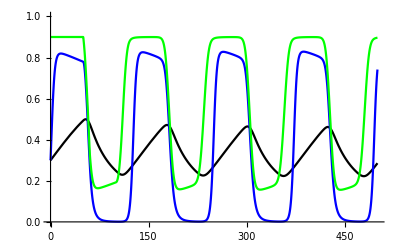

```mathematica
Plot[{x1[t]/.dsol,x2[t]/.dsol,h[t]/.dsol},{t,0,tmax},PlotRange->{0,1.},PlotStyle->{Black,Blue,Green}]
```

### Análise analítica

```mathematica
parametros={c1->0.04,c2->0.7,e1->0.01,e2->0.01,tr->10,to->50,g->0.1};
dx1=(c1* x1(h-x1)-e1 x1);
dx2=(c2 x2(h-x1-x2+x1*x2)-e2 x2);
sol=Solve[dx1==0 && dx2==0,{x1,x2}];
M={{D[(dx1), x1],D[(dx1), x2]},{D[(dx2), x1],D[(dx2), x2]}};
(*MatrixForm[M]sol*)
```

```mathematica
MA=M/.sol[[4]]/.parametros(*/.h->0.5*);
P=CharacteristicPolynomial[MA,l]
Roots[P==0,l]
```

```mathematica
Plot[Im[√(0.024024999999999998+0.012399999999999998 h+0.0016 h^2)],{h,0,1}]
```

```mathematica
A=2;
AV=Eigenvalues[M]/.sol[[A]]/.parametros;
{Plot[{AV[[1]],AV[[2]]},{h,0.,1.}],    Plot[{sol[[A]][[1]][[2]]/.parametros,sol[[A]][[2]][[2]]/.parametros},{h,0.,1.},PlotStyle->{Black,Blue},PlotLegends->{"Guanaco","Ovelha"}]}
```